# Integration of various coupled scalar-GB-eqs with radial perturbation

This notebook is aimed to study the stability of BH solutions in quartic-scalar-GB theory under radial perturbations.

```mathematica
Quit[];
```

### Needed files

files Needed

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Loading the system of equations from auxiliary file*)
perturbEQS=Import["Needed Files/general_perturb_GBeqs.m"]; (*file containing the perturbed equation obtained by the notebook used in article 1903.06784_Gualtieri*)
backEQS=Import["Needed Files/general_background_eqs.m"];
perturbedSCH=Import["Needed Files/Schwarz_perturb_GBeqs.m"]; (*Perturbed equation for Schwarzschild background*)
perturbedSCHϕ0=Import["Needed Files/Schwarz_perturb_GBeqs_generalϕ0value.m"];
```

```mathematica
(*Load packages for numerical integration*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

```mathematica
audio=Audio[File["/home/dario/Downloads/Y2meta.app - Stop Wait a minute sound effect (128 kbps).mp3"]];
```

#### Importing data

```mathematica
(*Extracts the part of the table corresponding to scalarized solution,giving the corresponding values of η,λ,Subscript[ϕ, h],M,Q*)
```

```mathematica
(*ReadList["Data/etaFund_lambda=0.5η.dat"];
TAB=quarticBranch;
tabelQ={};
tab07Q={};
Do[If[TAB[[i,3]]>0,Massa=( TAB[[i,4]]);tabelQ=AppendTo[tabelQ,{TAB[[i,1]],TAB[[i,2]],TAB[[i,3]],Massa,TAB[[i,5]]*Massa}]],{i,1,Length[TAB]}];
Do[If[tabelQ[[i,1]]<=0.726,(*Print["η=", tabel[[i,1]] ," ","Massa=" ,tabel[[i,3]], " ","Q=", tabel[[i,4]]];*)tab07Q=AppendTo[tab07Q,tabelQ[[i]]]],{i,1,Length[tabelQ]}]
nomefile=StringJoin[{"Data/FundBranch_λ=0.5η.m"}];
Save[nomefile,tab07Q];*)
```

```mathematica
FundExpA1d5=ReadList["Data/Branches/Exponential/Fund_Exponential_a=1.5.dat"][[1]]; (*Fundamental branch of Exponential coupling, a=3/2*)
FundPhi3=ReadList["Data/Branches/Phi3FundBranch.m"][[1]]; (*Fundamental branch with λ=-0.5η meaning it is stable *)
FundQuarticOnly=ReadList["Data/Branches/QuarticFundBranch.m"][[1]]; (*Fundamental branch of quartic only coupling*)
FundTwoThree=ReadList["Data/Branches/FundTwoThree_λ=-η.dat"][[1]];
(*Fundamental branch of polynomial coupling with powers 2 and 3*)
FundTwoThreeUnst=ReadList["Data/Branches/FundTwoThree_λ=1η.dat"][[1]];
(*Fundamental branch of polynomial coupling with powers 2 and 3*)
FundExpA3=ReadList["Data/Branches/Exponential/Fund_Exponential_a=3.dat"][[1]];
(*Fundamental branch of Exponential coupling, a=3*)
FundExpA6=ReadList["Data/Branches/Exponential/Fund_Exponential_a=6.dat"][[1]];
(*Fundamental branch of Exponential coupling, a=6*)
FundQuadratic=ReadList["Data/Branches/QuadraticFundBranch.m"][[1]];(*Pure quadratic function, fundamental branch*)
FundExpPow3=ReadList["Data/Branches/Exponential/NO_Fund_Exponential_a=10pow3.dat"][[1]];(*Exponential coupling with variable a=(10+η)^(1/3)*)
FundExpA2=ReadList["Data/Branches/Exponential/Fund_Exponential_a=2.dat"][[1]];
FundExpA4=ReadList["Data/Branches/Exponential/Fund_Exponential_a=4.dat"][[1]];
FundExpA5=ReadList["Data/Branches/Exponential/Fund_Exponential_a=5.dat"][[1]];
FundExpA7=ReadList["Data/Branches/Exponential/Fund_Exponential_a=7.dat"][[1]];
FundExpA8=ReadList["Data/Branches/Exponential/Fund_Exponential_a=8.dat"][[1]];
FundExpA9=ReadList["Data/Branches/Exponential/Fund_Exponential_a=9.dat"][[1]];
FundExpA10=ReadList["Data/Branches/Exponential/Fund_Exponential_a=10.dat"][[1]];
FundExpA20=ReadList["Data/Branches/Exponential/Fund_Exponential_a=20.dat"][[1]];
FundExpA30=ReadList["Data/Branches/Exponential/Fund_Exponential_a=30.dat"][[1]];
FundExpA40=ReadList["Data/Branches/Exponential/Fund_Exponential_a=40.dat"][[1]];
FundExpA50=ReadList["Data/Branches/Exponential/Fund_Exponential_a=50.dat"][[1]];
FundExpA60=ReadList["Data/Branches/Exponential/Fund_Exponential_a=60.dat"][[1]];
FundExpA70=ReadList["Data/Branches/Exponential/Fund_Exponential_a=70.dat"][[1]];
FundExpA80=ReadList["Data/Branches/Exponential/Fund_Exponential_a=80.dat"][[1]];
FundExpA90=ReadList["Data/Branches/Exponential/Fund_Exponential_a=90.dat"][[1]];
FundExpA100=ReadList["Data/Branches/Exponential/Fund_Exponential_a=100.dat"][[1]];
FundExpA1000=ReadList["Data/Branches/Exponential/Fund_Exponential_a=1000.dat"][[1]];

FundLorentz005=ReadList["Data/Branches/Fund_Lorentz_a=0.05.dat"][[1]];
FundLorentz001=ReadList["Data/Branches/Fund_Lorentz_a=0.01.dat"][[1]];
```

## Background fields integration

In this case we write the metric ds2 = −A(r)dt^2+ (B(r))^-1 dr^2 + r^2 dΩ^2. 
Now we simplify the background diff equations imposing α=1/2 and that we want a simple theory with no scalar field potential

```mathematica
BEQS=Simplify[backEQS//.{Vf->(0&),α->1/2}];
```

```mathematica
(*Define the coupling function we will study.*)
```

```mathematica
(*ruleCoupling={F-> ((η/8#^2+λ/16#^4)&)};*)
ruleThird={F-> ((η/12#^3)&)};
ruleExponential={F->((η/(4*2a)(1-Exp[-a#^2]))&)};
ruleQuartic={F-> ((η/16#^4)&)};
ruleQuadratic={F-> ((η/8#^2)&)};
ruleTwoThree={F-> ((η/8#^2+λ/12#^3)&)};
ruleTwoFour={F-> ((η/8#^2+λ/16#^4)&)};
ruleLorentzian={F->(η/8 a^3(1/a-a/(#^2+a^2))&)};
```

```mathematica
Rh=1;(*Setting the event horizon value*)
```

### Background Boundary conditions

```mathematica
BCSbckHor=<<"Needed Files/expanded_bck_BCS_hor.m";
```

Boundary condition for the background at the horizon. We shall consider only terms up to second order.

```mathematica
bouhor={Sum[Subscript[ai, i](r-1)^i,{i,1,2}],Sum[Subscript[bi, i](r-1)^i,{i,1,2}],Sum[Subscript[fi, i](r-1)^i,{i,0,2}],D[Sum[Subscript[fi, i](r-1)^i,{i,0,2}],r]};
```

### Background Integration

I’ll work with compactified coordinate x=1-rh/r so that the event horizon is mapped at x->0 and r->∞ is at x->1

```mathematica
(*CBEQ are the background equations in compactified coordinates*)
```

```mathematica
CBEQ=(1-x)^3 BEQS/.{A->(A[1-Rh/#]&),B->(B[1-Rh/#]&),ϕ->(ϕ[1-Rh/#]&)}/.r->Rh/(1-x)//Simplify;
```

```mathematica
Clear[CsGBINT];
```

CsGBINT:   (rh, ϕh, η, λ, rmax, Nh, ruleCoupling, ) ->  (ϕinf, ϕ[r],ϕ'[r],A[r],A'[r],B[r],B'[r],ϕ0,Q/M, η/M^2,λ/M^2,M )   Integration of the equations for a given choice of rh, ϕh, η, λ

```mathematica
CsGBINT[phic0_,coupConst_,xmax0_,xinf_,MODEL_,ϵ0_]:=(
rh0=1;
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->13,AccuracyGoal->13,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*ϵ0 difines how far from the horizon we will start our integrations*)

(*Initial conditions*)
(*Georgios' way*)
BChorrule=BCSbckHor//.MODEL;
ruBChor=BChorrule//.coupConst/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOU=Thread[{A[x],B[x],ϕ[x],(-1+x)^2 ϕ'[x]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0/.r->1/(1-x))]/.x->ϵ0;

BCS=BOU;
(*Numerical integration*)
sol=NDSolve[
Union[Union[{CBEQ[[2]]==0,CBEQ[[1]]==0, CBEQ[[3]]==0}//.MODEL/.coupConst],BCS],
{A,B,ϕ},
{x,ϵ0,xmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsol=ϕ[x]/.sol;
Dϕsol=D[ϕsol,x];
Asol=A[x]/.sol;
DAsol=D[Asol,x];
Bsol=B[x]/.sol;
DBsol=D[Bsol,x];
(*Values of variables at infinity*)
ϕinf=ϕsol/.{x-> xmax0};
Ainf=Asol/.{x-> xmax0};
Binf=Bsol/.{x-> xmax0};
Asolshift=Asol/Ainf;


PhysicalParams=NSolve[{
Asolshift==1-(2 M)/r+((M Q^2)/(12 r^3)),
ϕsol==ϕ0+Q/r+(M Q)/r^2+((32 M^2 Q-Q^3)/(24 r^3)),
((1-x)^2/rh0)D[ϕsol,x]==D[ϕ0+Q/r+(M Q)/r^2,r]&&M≥ 0 }/.r->rh0/(1-x)/.{x->xinf},{ϕ0,Q,M}][[1]];

(*Output: ϕinf, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r], ϕ0, Q/M, M*)
{ϕinf,
ϕsol,
Dϕsol,
Asol*(1/Ainf),
DAsol*(1/Ainf),
Bsol(*/Binf*),
DBsol(*/Binf*),
ϕ0/.PhysicalParams,
(Q/M)/.PhysicalParams,
M/.PhysicalParams
}
);
```

I also report the integration in radial coordinate which is useful then for the effective potential study and to have the constant Wronskian for the perturbed eq. solutions

```mathematica
sGBINT[phic0_,coupConst_,rmax0_,NHorizons0_,MODEL_,ϵ0_]:=(
rh0=1;
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->20,AccuracyGoal->20,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*Initial conditions*)
(*Georgios' way*)
BChorrule=BCSbckHor//.MODEL;
ruBChor=BChorrule//.coupConst/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOUr=Thread[{A[r],B[r],ϕ[r],ϕ'[r]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0)]/.r->rh0+ϵ0;

BCSr={
A[r]==N[r-rh],
B[r]==N[r-rh],
ϕ'[r]==N[(rh/(4 F'[ϕ[r]]))(-1+Sqrt[1-96 ((F'[ϕ[r]])^2/rh^4)])]//.Union[MODEL,{η->η0, λ->λ0}],
(*condizione necessaria affinché ϕ'' non diverga all'orizzonte.*)
ϕ[r]==phic0
}/.coupConst//.{r->rh0+ϵ0,rh-> rh0,ϕ[rh]->phic0};

BCSr=BOUr;
(*Numerical integration*)
solr=NDSolve[
Union[Union[{BEQS[[2]]==0,BEQS[[1]]==0, BEQS[[3]]==0}//.MODEL/.coupConst],BCSr],
{A,B,ϕ},
{r,rh0+ϵ0,rmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsolr=ϕ[r]/.solr;
Dϕsolr=D[ϕsolr,r];
Asolr=A[r]/.solr;
DAsolr=D[Asolr,r];
Bsolr=B[r]/.solr;
DBsolr=D[Bsolr,r];
(*Values of variables at infinity*)
ϕinfr=ϕsolr/.{r-> rmax0};
Ainfr=Asolr/.{r-> rmax0};
Binfr=Bsolr/.{r-> rmax0};
Asolshiftr=Asolr/Ainfr;
DAsolshiftr=DAsolr/Ainfr;
Bsolshiftr=Bsolr/Binfr;
DBsolshiftr=DBsolr/Binfr;

(*Extract physical parameters of the BH solution*)
PhysicalParams=NSolve[{
Asolshiftr==1-(2 Mr)/r+((Mr *Qr^2)/(12 r^3)),
ϕsolr==ϕ0r+Qr/r+(Mr* Qr)/r^2+((32 Mr^2 Qr-Qr^3)/(24 r^3)),
D[ϕsolr,r]==D[ϕ0r+Qr/r+(Mr* Qr)/r^2,r]&&Mr≥ 0 }/.{r->rh0*NHorizons0},{ϕ0r,Qr,Mr}][[1]];

(*NOTA: entrambe le costanti di accoppiamento η e λ hanno (dimensione [length])^2, mentre il campo scalare à adimensionale in tale trattazione e lo scalare di Gauss-Bonnet (è [length])^-4*)
(*Nell'output restituisco l'esponenziale delle funzioni metriche Υ e Λ, che chiamo A[r] e B[r]*)

(*Output: ϕ0, ϕinf, Q/M, M, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r]*)
{ϕ0r/.PhysicalParams,
ϕinfr,
(Qr/Mr)/.PhysicalParams,
Mr/.PhysicalParams,
ϕsolr,
Dϕsolr,
Asolshiftr,
DAsolshiftr,
Bsolshiftr,
DBsolshiftr
}
);
```

## Perturbed integration

### Perturbed equations

I’m interested in the simplest case where the potential Vf = 0. Moreover the perturbEQS has a constant value α which can be set to 1/2 for the whole analysis: in fact it varies depending on the metric used for the background field integration, i.e.  if the metric functions are defined as exp(Υ) or exp(2Υ), etc.

The equation we need is the following: - ∂^2 φ1/∂r^2  + h(r) ∂^2 φ1/∂t^2 + k(r)∂φ1/∂r +p(r)φ1=0. In perturbEQS we have this equation but in a more general form, so we have to simplify it a little for our problem.

```mathematica
(*Salcedo's equations*)
```

```mathematica
PEQS=Simplify[perturbEQS//.{Vf[ϕ[r]]->0, Vf'[ϕ[r]]->0,Vf''[ϕ[r]]->0,α->1/2}];
```

```mathematica
PEQSom=PEQS/.ϕ1->(φ[#2]Exp[-I ω #1]&)/.t->0//Simplify;
```

```mathematica
CPEQS=PEQSom/.{A->(A[1-1/#]&),B->(B[1-1/#]&),ϕ->(ϕ[1-1/#]&),φ->(φ[1-1/#]&)}/.r->Rh/(1-x)//Simplify;
(*toNorm=Coefficient[CPEQS,φ''[x]];
CPEQS2=CPEQS/toNorm//Simplify;*)
```

```mathematica
(*for the Schwarzschild background*)
```

```mathematica
CPEQsch=perturbedSCH/.Vf->(0&)/.α->1/2/.ϕ1->((φ[#2]Exp[-I ω #1])&)/.t->0/.φ->(φ[1-1/#]&)/.r->1/(1-x)//Simplify
```

1/(-1+x)^6(-(-1+x)^4 x (1-288 (-1+x)^5 F'[0]^2-336 (-1+x)^6 F'[0]^2) φ'[x]+(1-x)^3 φ[x] (x-288 (-1+x)^5 F'[0]^2-528 (-1+x)^6 F'[0]^2-240 (-1+x)^7 F'[0]^2+12 (-1+x)^3 F''[0]+12 (-1+x)^4 F''[0])-(1-48 (-1+x)^6 F'[0]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))

```mathematica
CPEQschϕ0=perturbedSCHϕ0/.Vf->(0&)/.α->1/2/.ϕ1->((φ[#2]Exp[-I ω #1])&)/.t->0/.φ->(φ[1-1/#]&)/.r->1/(1-x)/.ϕ0->ϕz//Simplify
```

1/(-1+x)^6(-(-1+x)^4 x (1-48 (-1+x)^5 (-1+7 x) F'[ϕz]^2) φ'[x]+(1-x)^3 x φ[x] (1-48 (-1+x)^5 (1+5 x) F'[ϕz]^2+12 (-1+x)^3 F''[ϕz])-(1-48 (-1+x)^6 F'[ϕz]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))

```mathematica
(*
(CPEQschϕ0/.ruleCoupling/.ϕz->0)==CPEQsch/.ruleCoupling//Simplify*)
```

### Integration functions

#### Schwarzschild BH background

```mathematica
ϕ0Finding[MODEL_]:=(
Clear[couple];
couple[ϕz_]:=F[ϕz]/.MODEL;
SchSol=Solve[{couple'[ϕz]==0,ϕz!=0},ϕz];
SchSol
);
```

INPUT:  rh, {coupling constants}, coupling function,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

```mathematica
PINTEGschϕ0[coupConst_,MODEL_,ω0_,xm_ ,ϵ0_,choosesol_]:=(
rh0=1;
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,(*PrecisionGoal->10,*)AccuracyGoal->20,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

(*ϵ0 tells how far from the horizon we will start our integrations*)
xmin=ϵ0;
xinf=0.99;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*we choose which solution of the equation F'[ϕ]=0 to take: if choosesol=0 -> ϕh=0 else ϕh=ϕ0Finding*)
If[choosesol==0, phi0=(ϕz->0),phi0=ϕ0Finding[MODEL][[1]]];

CPEQschw=CPEQschϕ0/.MODEL/.phi0;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSminSCH={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};

(*Boundary conditions for the integration towards infinity*)
PBCSplusSCH={
φ[x]==0(*φSCH//.x->xmax*),
φ'[x]==cons(*DφSCH/.x->xmax*)
}//.{x->xinf, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}/.coupConst},PBCSminSCH],φ,
{x,xmin,xm+ϵ0},
rulePAR];
SOLplusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}/.coupConst},PBCSplusSCH],φ,
{x,xinf,xm-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminusSCH=φ[x]/.SOLminusSCH;
DφminusSCH=D[φminusSCH,x];
φplusSCH=φ[x]/.SOLplusSCH;
DφplusSCH=D[φplusSCH,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminusSCH(*/(φminusSCH/.x->xm)*),
DφminusSCH(*/(φminusSCH/.x->xm)*),
φplusSCH(*/(φplusSCH/.x->xm)*),
DφplusSCH(*/(φplusSCH/.x->xm)*)}

);
```

INPUT:  rh, {coupling constants}, coupling function,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

```mathematica
PINTEGsch[coupConst_,MODEL_,ω0_,xm_ ,ϵ0_]:=(
rh0=1;
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,(*PrecisionGoal->10,*)AccuracyGoal->20,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

(*ϵ0 tells how far from the horizon we will start our integrations*)
xmin=ϵ0;
xinf=0.99;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.*)

CPEQschw=CPEQsch/.MODEL/.coupConst;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSminSCH={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};

(*Boundary conditions for the integration towards infinity*)
PBCSplusSCH={
φ[x]==0(*φSCH//.x->xmax*),
φ'[x]==cons(*DφSCH/.x->xmax*)
}//.{x->xinf, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}},PBCSminSCH],φ,
{x,xmin,xm+ϵ0},
rulePAR];
SOLplusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplusSCH],φ,
{x,xinf,xm-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminusSCH=φ[x]/.SOLminusSCH;
DφminusSCH=D[φminusSCH,x];
φplusSCH=φ[x]/.SOLplusSCH;
DφplusSCH=D[φplusSCH,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminusSCH(*/(φminusSCH/.x->xm)*),
DφminusSCH(*/(φminusSCH/.x->xm)*),
φplusSCH(*/(φplusSCH/.x->xm)*),
DφplusSCH(*/(φplusSCH/.x->xm)*)}

);
```

```mathematica
PINTEGsch[η->0.8,ruleQuadratic,0.1,0.5,10^-15]
```

{{InterpolatingFunction[…][x]},{InterpolatingFunction[…][x]},{InterpolatingFunction[…][x]},{InterpolatingFunction[…][x]}}

#### Scalarized BH solutions

INPUT:  rh,  ϕh,  η,  λ,  rmax[r],  Nhorizons,  ruleCoupling,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

note:  rh is always set to 1; rmax is given in r and it’s used for the CsGBINT, same as Nhorizons;  ωi is the Imaginary part of the frequency (Real number)

```mathematica
PINTEGx[phic0_,coupConst_,rmax0_,NHorizons0_,MODEL_, ω0_,xm_,xmin_,xmax_,precision_ ]:=(
rh0=1;
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,PrecisionGoal->precision,AccuracyGoal->precision,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};
ϵ0=xmin;
ϵ2=10^-15;(*How far from the horizon we will start our integrations*)
(*xmin=ϵ0;*)
(*xmax=0.99;*)
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=1;

(*Defining the background metric functions AA[r], BB[r] and the background field Φ[t,r]
We rewrite input and output of the sGBINT to remember
Input: ϕh,couplingConstants,rmax,Nh,rule
	output: ϕ0, Φinf, Q/M, M, Φsol, DΦsol, A[r], A'[r], B[r], B'[r]*)

(*BCKGRNDr=sGBINT[phic0,coupConst,rmax0,NHorizons0,MODEL,ϵ2];*)
BCKGRND=CsGBINT[phic0,coupConst,1-1/rmax0,1-1/NHorizons0,MODEL,xmin];
AA=BCKGRND[[4]];
BB=BCKGRND[[6]];
ϕbck=BCKGRND[[2]];

ruleCOEFF={A[x]->AA, A'[x]->D[AA,x],A''[x]->D[D[AA,x],x],B[x]->BB,B'[x]->D[BB,x],B''[x]->D[D[BB,x],x],ϕ[x]->ϕbck,ϕ'[x]->D[ϕbck,x],ϕ''[x]->D[D[ϕbck,x],x]};

(*CPEQ is the perturbed diff eq depending on x, the one we will integrate*)
CPEQ=CPEQS/.MODEL/.coupConst/.rh->rh0/.(*sol*)ruleCOEFF;

PEQ=PEQSom/.MODEL/.coupConst/.{rh->rh0}/.solr;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate as first approximation*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSmin={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};


(*Boundary conditions for the integration towards infinity*)
PBCSplus={
φ[x]==0(*/.x->xmax*),
φ'[x]==cons(*/.x->xmax*)
}//.{x->xmax, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSmin(*us*)],φ,
{x,xmin,xm(*+0.3*)+ϵ0},
rulePAR];
SOLplus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplus],φ,
{x,xmax,xm(*-0.3*)-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminus=φ[x]/.SOLminus;
Dφminus=D[φminus,x];
φplus=φ[x]/.SOLplus;
Dφplus=D[φplus,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminus/(φminus/.x->xm),
Dφminus/(φminus/.x->xm),
φplus/(φplus/.x->xm),
Dφplus/(φplus/.x->xm)}

);
```

```mathematica
(*numero=1;
xm=0.5;
tab=FundExp;
ruleCoupling=ruleExponential;
eta=tab[[numero,1]];
cou={η->eta,a->3/2};
phih=tab[[numero,2]];
outx=PINTEGx[phih,cou,10^12,150,ruleCoupling,0.09,xm,10^-8];
phiminDx=outx[[1]];
phipluDx=outx[[3]];
DphiminDx=outx[[2]];
DphipluDx=outx[[4]];
(phiminDx/DphiminDx-phipluDx/DphipluDx)/.x->xm*)
```

```mathematica
(*GraphicsRow[{Plot[phiminDx,{x,xmin,xm},PlotRange->Full,PlotLabel->Style[Framed["φ^(-)"],16,Blue]],
Plot[DphiminDx,{x,xmin,xm},PlotRange->Automatic,PlotLabel->Style[Framed["Dφ^(-)"],16,Blue]]}]
GraphicsRow[{Plot[phipluDx,{x,xm,xmax},PlotRange->Full,PlotLabel->Style[Framed["φ^(+)"],16,Red]],
Plot[DphipluDx,{x,xm,xmax},PlotRange->Full,PlotLabel->Style[Framed["Dφ^(+)"],16,Red]]}]
(*Plot[φSCH,{x,xmax,xinf},PlotRange->Full]*)
phiminDx/DphiminDx-phipluDx/DphipluDx/.x->0.5*)
```

### Tortoise coordinate and Effective potential

#### Constant Wronskian

I want to compute the solution in the tortoise coordinate R defined as dR/dr=g, where g is the square root of the coefficient of the perturbed differential equation written in this way:
g^2 (∂^2 φ)/(∂t^2)-(∂^2 φ)/(∂r^2)+C (∂φ)/(∂r)+Uφ=0, so in our case (g^2) =-Hr/Nr. In this way I can write the differential equation in this form (-d^2/dR^2+ Veff)Z=ω^2Z and so that the Wronskian computed with respect to the tortoise coordinate is constant. Z is such that φ=F * Z and F satisfies the equation (2F')/F=C-g'/g with all this functions dependent on r

```mathematica
(*numero=1;
xm=0.5;
tab=FundInsta;
eta=tab[[numero,1]];
lambda=tab[[numero,2]];
phih=tab[[numero,3]];
outx=PINTEGx[Rh,phih,eta,lambda,10^12,150,ruleCoupling,0.09,xm,10^-8];
phimin=outx[[1]];
phiplus=outx[[3]];
Dphimin=outx[[2]];
Dphiplus=outx[[4]];*)
```

```mathematica
(*GraphicsRow[{Plot[phimin,{x,2*10^-16,xm+0.3}],Plot[phiplus,{x,xm-0.3,0.99}]}]*)
```

```mathematica
(*coefome=Coefficient[PEQ,ω^2];*)
```

```mathematica
(*PEQ2=PEQ/.ω->0(*//Simplify*);*)
```

```mathematica
(*PEQ2==PEQ-coefome*ω^2;*)
```

```mathematica
(*coef=Coefficient[PEQ2,{φ[r],φ'[r],φ''[r]}];
coefC=coef[[2]];(*k*)
coef1=coef[[3]];(*n*)
coefU=coef[[1]];(*p*)
coefg=Coefficient[coefome,φ[r]];(*-h: lui è -h perché derivando 2 volte rispetto al tempo porto giù un (-I)^2 e h era preso invece prima di derivare*)*)
```

```mathematica
(*Plot[{-coef1/coef1,-coefC/coef1,-coefU/coef1,-coefg/coef1},{r,1,10}]*)
```

```mathematica
(*(*Defining coefficients functions as in Doneva's paper*)
g[rr_]:=Sqrt[(coefg/coef1)]/.r->rr//Simplify;
c[rr_]:=-coefC/coef1/.r->rr//Simplify;
u[rr_]:=-coefU/coef1/.r->rr//Simplify;
*)
```

```mathematica
(**)
```

```mathematica
(*Plot[g[rr],{rr,1.1,3},PlotRange->Full]*)
```

```mathematica
(*(*this is the differential equation that the function ff[r] (difined by φ[r]=ff[r]Z[r]) must satisfy*)
Clear[eqtortoise];
eqtortoise[rr_]:=(2fun'[rr]/fun[rr]-c[rr]+g'[rr]/g[rr]);*)
```

```mathematica
(*(*integration*)
BCfun=fun[Rh+10^-6]==1;
SOLfun=NDSolve[{eqtortoise[rr]==0,BCfun},fun,{rr,1+10^-5,20},rulePAR][[1]];
ff[rr_]:=fun[rr]/.SOLfun;
*)
```

```mathematica
(*Plot[{ff[rr]},{rr,Rh+10^-2,3},PlotRange->Full]*)
```

```mathematica
(*DChange[x_]:=(1-x)^2/Rh;*)
```

```mathematica
(*(*Passing again to r coordinate for the solutions that are computed in the compactified coordinate x*)
phiminr[rr_]:=phimin/.x->{1-Rh/rr};
Dphiminr[rr_]:=DChange[x]^-1*Dphimin/.x->{1-Rh/rr};
phiplur[rr_]:=phiplus/.x->{1-Rh/rr};
Dphiplur[rr_]:=DChange[x]^-1*Dphiplus/.x->{1-Rh/rr};*)
```

```mathematica
(*
(*Computing the Z^(-) and Z^(+) functions according to φ[r]=ff[r]Z[r]*)
Zmin[rr_]:=phiminr[rr]/ff[rr];
Zplus[rr_]:=phiplur[rr]/ff[rr];

(*Finally I can compute the Wronskian in tortoise coordinate, whose value doesn't depend on the matching point*)
WRO[rm_]:=g[rm]^-1(Zmin[rm]*Zplus'[rm]-Zplus[rm]*Zmin'[rm])(*/(ff[rm]^2 Zmin'[rm]*Zplus'[rm]+ff'[rm]*Zmin[rm]Zplus[rm])*);*)
```

```mathematica
(*Table[WRO[i][[1]],{i,2,5}]*)
```

```mathematica
(*Table[WROGG[i][[1]],{i,2,5}]*)
```

```mathematica
(*Plot[{WRO[rm],WROGG[rm]},{rm,1.25,5},PlotRange->{-10^-16,10^-9}]*)
```

```mathematica
(*Veff[rr_]:=g[rr]^-2 (u[rr]-ff''[rr]/ff[rr]-c[rr]/ff[rr] ff'[rr]);
CVeff[x_]:=Veff[rr]/.rr->Rh/(1-x);*)
```

```mathematica
(*Veff[5]*)
```

```mathematica
(*Plot[{Veff[rr],VeffG[rr]},{rr,1.0001,3}, PlotRange->Full]*)
```

```mathematica
(*Labeled[GraphicsRow[{Plot[Veff[rr],{rr,1.0001,10}, PlotRange->Full,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]](*,Plot[CVeff[x],{x,0.1,0.9}, PlotRange->Full]*)}],{"r/r_h","V_effr_h^2"},{Bottom,Left}]*)
```

```mathematica
(*WRO[5]*)
```

#### Effective potential

I want to study the effective potential for different coupling functions and verify if its integral in tortoise coordinate is negative or positive for a given coupling constant : in the first case this condition is sufficient to imply instability of the scalarized solution

```mathematica
IntPotentialSign[phihor_,const_,MODEL_,MaxInterpol_,precisionInterpol_,ϵ2_]:=(
RMAX=10^10;
NHOR=150;
(*Firstly I have to integrate the background field equations in order to compute the coefficients of the prturbed eq.*)

BkG=sGBINT[phihor,const,RMAX,NHOR,MODEL,ϵ2];
ruleCOEFFr={A[r]->Asolshiftr, A'[r]->DAsolshiftr,A''[r]->D[Asolshiftr,r],B[r]->Bsolshiftr,B'[r]->DBsolshiftr,B''[r]->D[DBsolshiftr,r],ϕ[r]->ϕsolr,ϕ'[r]->Dϕsolr,ϕ''[r]->D[Dϕsolr,r]};

PEQ=PEQSom/.MODEL/.const/.{rh->1}/.ruleCOEFFr;

(*The following is the coefficient of the term multiplying ω^2 in the perturbed equation, which corresponds to g when φ is set to 1*)
coefome=Coefficient[PEQ,ω^2];
(*Now I collect the coefficients of the 0 first and second derivative of the perturbed equation. I have to remove coefome because I want the φ term not to include ω^2*)
PEQ2=PEQ/.ω^2->0;
coef=Coefficient[PEQ2,{φ[r],φ'[r],φ''[r]}];
coefC=coef[[2]];(*k*)
coef1=coef[[3]];(*n*)
coefU=coef[[1]];(*p*)
coefg=Coefficient[coefome,φ[r]];

(*Defining coefficients functions as in Doneva's paper*)
gsquare[r_]:=coefg/coef1/.r->rr//Simplify;
g[rr_]:=Sqrt[(coefg/coef1)]/.r->rr//Simplify;
c[rr_]:=-coefC/coef1/.r->rr//Simplify;
u[rr_]:=-coefU/coef1/.r->rr//Simplify;

(*n[rr_]:=coef1/.r->rr//Simplify;
p[rr_]:=coefU/.r->rr//Simplify;
k[rr_]:=coefC/.r->rr//Simplify;*)

(*Since the function that we get are too difficult to differentiate, now we proceed with an interpolation*)
utab=Table[{r,u[r]},{r,1+ϵ2,MaxInterpol,precisionInterpol}];
gtab=Table[{r,g[r]},{r,1+ϵ2,MaxInterpol,precisionInterpol}];
ctab=Table[{r,c[r]},{r,1+ϵ2,MaxInterpol,precisionInterpol}];
g2tab=Table[{r,gsquare[r]},{r,1+ϵ2,MaxInterpol,precisionInterpol}];

gint=Interpolation[gtab,InterpolationOrder->20];
g2int=Interpolation[g2tab,InterpolationOrder->20];
cint=Interpolation[ctab,InterpolationOrder->20];
uint=Interpolation[utab,InterpolationOrder->20];

ui[rr_]:=uint[x]//.x->rr;
gi[rr_]:=gint[x]//.x->rr;
ci[rr_]:=cint[x]//.x->rr;

(*Now we write the expression for the effective potential in terms of these coefficients*)
Veff[rr_]:=1/gi[rr]^2(ui[rr]+ci[rr]^2/4-ci'[rr]/2-3/4(gi'[rr]/gi[rr])^2+gi''[rr]/(2gi[rr]))//Simplify;
(*Veff[rr_]:=-pf[rr]+kf[rr]^2/(4nf[rr])+kf'[rr]/2+nf'[rr]/(2nf[rr])(9/8 nf'[rr]-kf[rr])-nf''[rr]/4//Simplify;*)
(*
intVeff=NIntegrate[Veff[r]*gi[r],{r,1+precisionInterpol,MaxInterpol},AccuracyGoal->10];

intVeff*)
g2int
);
```

tentativo

```mathematica
(*IntPotentialSign[phihor_,const_,MODEL_,MaxInterpol_,precisionInterpol_,tab_,num_,omega_]:=(
RMAX=10^10;
NHOR=150;

(*Firstly I have to integrate the prturbed eq.*)
xm=0.5;
eta=tab[[num,1]];
lambda=tab[[num,2]];
phih=tab[[num,3]];
outx=PINTEGx[1,phih,eta,lambda,RMAX,NHOR,MODEL,omega,xm,10^-8];
phimin=outx[[1]];
phiplus=outx[[3]];
Dphimin=outx[[2]];
Dphiplus=outx[[4]];

(*The following is the coefficient of the term multiplying ω^2 in the perturbed equation, which corresponds to g when φ is set to 1*)
coefome=Coefficient[PEQ,ω^2];
(*Now I collect the coefficients of the 0 first and second derivative of the perturbed equation. I have to remove coefome because I want the φ term not to include ω^2*)
PEQ2=PEQ/.ω^2->0;
coef=Coefficient[PEQ2,{φ[r],φ'[r],φ''[r]}];
coefC=coef[[2]];(*k*)
coef1=coef[[3]];(*n*)
coefU=coef[[1]];(*p*)
coefg=Coefficient[coefome,φ[r]];

(*Defining coefficients functions as in Doneva's paper*)
g[rr_]:=Sqrt[(coefg/coef1)]/.r->rr//Simplify;
c[rr_]:=-coefC/coef1/.r->rr//Simplify;
u[rr_]:=-coefU/coef1/.r->rr//Simplify;

(*this is the differential equation that the function ff[r] (difined by φ[r]=ff[r]Z[r]) must satisfy*)
Clear[eqtortoise];
eqtortoise[rr_]:=(2fun'[rr]/fun[rr]-c[rr]+g'[rr]/g[rr]);
(*integration for fun*)
BCfun=fun[1+10^-6]==1;
SOLfun=NDSolve[{eqtortoise[rr]==0,BCfun},fun,{rr,1+10^-5,20},rulePAR][[1]];
ff[rr_]:=fun[rr]/.SOLfun;

DChange[x_]:=(1-x)^2/Rh;
(*Passing again to r coordinate for the solutions that are computed in the compactified coordinate x*)
phiminr[rr_]:=phimin/.x->{1-Rh/rr};
Dphiminr[rr_]:=DChange[x]^-1*Dphimin/.x->{1-Rh/rr};
phiplur[rr_]:=phiplus/.x->{1-Rh/rr};
Dphiplur[rr_]:=DChange[x]^-1*Dphiplus/.x->{1-Rh/rr};

(*Computing the Z^(-) and Z^(+) functions according to φ[r]=ff[r]Z[r]*)
Zmin[rr_]:=phiminr[rr]/ff[rr];
Zplus[rr_]:=phiplur[rr]/ff[rr];

(*Now we write the expression for the effective potential in terms of these coefficients*)
Veff[rr_]:=g[rr]^-2 (u[rr]-ff''[rr]/ff[rr]+c[rr]/ff[rr] ff'[rr])//Simplify;
(*Veff[rr_]:=-pf[rr]+kf[rr]^2/(4nf[rr])+kf'[rr]/2+nf'[rr]/(2nf[rr])(9/8 nf'[rr]-kf[rr])-nf''[rr]/4//Simplify;*)

(*intVeff=NIntegrate[Veff[rr]*gi[rr],{rr,1+precisionInterpol,MaxInterpol},AccuracyGoal->5];

intVeff*)
);*)
```

## Shooting method with Wronskian

Here we search for the eigenvalue ωi corresponding to the frequency at which the Wronskian W = [φ^(-)(dφ^(+)/dx)- (dφ^(-)/dx) φ^(+)]_(x=x_m) vanishes

### Schwarzschild BH

```mathematica
WRONSKsch[const_, ω0_, xm_,ϵ0_,MODEL_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=PINTEGsch[const,MODEL,ω0,xm,ϵ0];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=((phimin/Dphimin-phiplu/Dphiplu)/.x->xm)[[1]]; (*Georgios definition*)
Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];

{Wrons1(*,
Wrons2,
prod*)}
);
WRONSKschϕ0[const_, ω0_, xm_,ϵ0_,choosesol_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=PINTEGschϕ0[const,ruleCoupling,ω0,xm,ϵ0,choosesol];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=((phimin/Dphimin-phiplu/Dphiplu)/.x->xm)[[1]]; (*Georgios definition*)
Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];

{Wrons1(*,
Wrons2,
prod*)}
);
```

```mathematica
CPEQsch/.ruleQuadratic
```

((1-x)^3 (x+3 (-1+x)^3 η+3 (-1+x)^4 η) φ[x]-ω^2 φ[x]-(-1+x)^4 x φ'[x]-(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x]))/(-1+x)^6

```mathematica
CPEQsch/.(F->(0&))
```

((1-x)^3 x φ[x]-ω^2 φ[x]-(-1+x)^4 x φ'[x]-(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x]))/(-1+x)^6

```mathematica
CPEQsch
```

1/(-1+x)^6(-(-1+x)^4 x (1-288 (-1+x)^5 F'[0]^2-336 (-1+x)^6 F'[0]^2) φ'[x]+(1-x)^3 φ[x] (x-288 (-1+x)^5 F'[0]^2-528 (-1+x)^6 F'[0]^2-240 (-1+x)^7 F'[0]^2+12 (-1+x)^3 F''[0]+12 (-1+x)^4 F''[0])-(1-48 (-1+x)^6 F'[0]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))

```mathematica
si=η->0.9;
```

```mathematica
WRONSKsch[si,1,0.5,10^-15,ruleQuadratic][[1]]
```

0.245638

```mathematica
0.5/100000000
```

5.×10^-9

```mathematica
ruleQuartic
```

{F→((η #1^4)/16&)}

Here in green there is the routine that computes the Wronskian for different values of ωi for every coupling parameters value and for Sch. Background.
I checked the last value of η at which we have scalarized solution up to the forth decimal place is ηi=0.7256

```mathematica
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=800;

ruleCoupling=ruleQuartic;

wi=0.0018;
wf=2;
step=(wf-wi)/pts;

ηi=1000000;
ηf=1000000000;
λmultiplier=-1.5;
epts=25;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
etap[z_]:=ηi+(ηf-ηi)/epts(z-1);
(*tab=SchwBckSol;*)
(*choosesoln=1;*)

xnear=2*10^-16;
minimaSch={};
Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
WROGsch[k]={};
ηk=etap[k];
λk=λmultiplier*ηk;
constants={η->ηk(*,λ->λk*)};
Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSKsch[constants,ωshoot,xmiddle,xnear,ruleCoupling][[1]];
WROGsch[k]=AppendTo[WROGsch[k],{ωshoot,check}]},{j,1,pts}],j];
min=Min[Table[WROGsch[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WROGsch[k]//Abs,min][[1,1]];
omegaok=WROGsch[k][[pos,1]];
minimaSch=AppendTo[minimaSch,{ηk,omegaok}]
,{k,1,epts}]
,k];
```

```mathematica
epts
```

25

```mathematica
check
```

0.219688

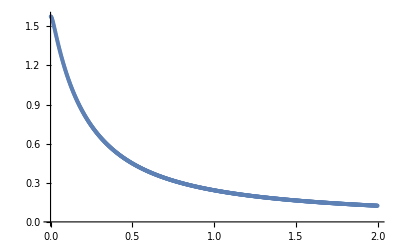
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

0.907552

```mathematica
Table[ListPlot[WROGsch[i]],{i,1,epts}]
```

```mathematica
minimaSch
```

{{0.7256,2.99725},{0.816576,2.99725}}

```mathematica
(*check*)
```

```mathematica
(*Table[ListPlot[WROGsch[i]],{i,1,epts}]*)
```

### Scalarized BH

```mathematica
WRONSK[phih0_,coupConst_,MODEL_, ω0_, xm_,xmin_,xmax_,precision_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=PINTEGx[phih0,coupConst,10^12,150,MODEL,ω0,xm,xmin,xmax,precision];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=(((phimin/Dphimin-phiplu/Dphiplu)(**Dphimin*Dphiplu*))/.x->xm)[[1]]; (*Georgios definition*)
(*Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];
*)
{Wrons1(*,
Wrons2,
prod*)}
);
```

Here in orange there is the routine that computes the Wronskian for different values of ωi for every coupling parameters value

#### Exponential coupling

Doneva says that for M/√η < 0.171=M_crit  scalarized solutions for exponential coupling with a=3/2 are unstable. We are going to check if we have the same behaviour for different values of a

```mathematica
PosMcrit[tab_,Mcrit_]:=(For[i=1,i<Length[tab],i++,
Madimensional=tab[[i,3]]/(tab[[i,1]]^(1/2));
(*Print[i," ",Madimensional];*)
If[Madimensional<Mcrit,position=i;Break[]]];
position
);
```

```mathematica
PosMcrit[FundExpPow3]
```

448

```mathematica
Length[tab]
```

1509

```mathematica
Clear[WROND]
```

```mathematica
(*xmmin=xmed[[Position[Wxmed,Min[Wxmed]][[1]]]]*)
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=1000;

wi=0.001;
wf=8;
step=(wf-wi)/pts;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
tab=FundExpA6;
ruleCoupling=ruleExponential;

xnear=10^-8;
xmax=0.99;
precision=8;

kstart=1160(*PosMcrit[tab]*);
divided=1;

a0=6; (*coefficient of ϕ^2 term at the exponent*)

(*minima={};*)

Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
k=kstart+divided*(l-1);
WROND[k]={};
ηk=tab[[k,1]];
(*λk=tab[[k,2]];*)
couple={η->ηk,a->a0};
phihk=tab[[k,2]];

Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSK[phihk,couple,ruleCoupling,ωshoot,xmiddle,xnear,xmax,precision](*[[1,1]]*);
WROND[k]=AppendTo[WROND[k],{ωshoot,check[[1]]}]}
,{j,1,pts}],j];
min=Min[Table[WROND[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WROND[k]//Abs,min][[1,1]];
omegaok=WROND[k][[pos,1]];
If[omegaok!=wi&&omegaok!=omeshoot[100],
minima=AppendTo[minima,{tab[[k,1]],omegaok, tab[[k,3]],tab[[k,4]]}];AudioPlay[audio],
Print["not yet", " ", k, " ", tab[[k,3]]/(tab[[k,1]]^(1/2))]],
{l,1,IntegerPart[(Length[tab]-kstart)/divided]}]
,k];
```

```mathematica
nomefile=StringJoin[{"Data/Stability/ExponentialA6_unstable.dat"}];
Save[nomefile,{WROND,minima}]
```

========================================================================================================================================================================================

```mathematica
Length[FundExpPow3]
```

1328

```mathematica
a0=6;
poscrit=PosMcrit[tabel,0.171/(a0/1.5)]
```

1092

Effective potential sign to determine instability

```mathematica
tabel=FundExpA90;

a0=90;
poscrit=PosMcrit[tabel,0.232449733*a0^-1];


coupling=ruleExponential;
ϵ=10^-6;
rstart=2.2;
rmax=15;
interpolPrecision=10^-2;
control=0;

toFit={};

Monitor[Do[
eta=tabel[[i,1]];
phi=tabel[[i,2]];
cost={η->eta,a->a0};
gsqrt=IntPotentialSign[phi,cost,coupling,rmax,interpolPrecision,ϵ];
toCheck=Table[g2int[ri],{ri,rstart,rmax-2*interpolPrecision,interpolPrecision}];
For[j=1,j<Length[toCheck]-1,j++,
sign=toCheck[[j]]*toCheck[[j+1]];
If[sign<0,
ErrMax=(tabel[[i-1,3]]/(tabel[[i-1,1]]^(1/2))-tabel[[i,3]]/(tabel[[i+1,1]]^(1/2)));
M=tabel[[i,3]]/(tabel[[i,1]]^(1/2));
Print["indice tabella=",i,",  ", "M/η^2=", " ",M, ", ", "Errore=", ErrMax, ",  η=" ,eta];
toFit=AppendTo[toFit,{a0,M,ErrMax}];
control=1;Break[]]];
If[control!=0,AudioPlay[audio];Break[]],
{i,poscrit-2,Length[tabel](*poscrit+5*),1}] ,i]
```

indice tabella=2869,  M/η^2= 0.00252811, Errore=9.0623×10^-6,  η=49240.

```mathematica
nomefile=StringJoin[{"Data/Stability/ExpoFIT/startEllipticity_fit.dat"}];
Save[nomefile,toFit]
```

```mathematica
M=tabel[[1349,3]]/(tabel[[1349,1]]^(1/2))
```

0.0692856

```mathematica
M=tabel[[1189,3]]/(tabel[[1189,1]]^(1/2))
```

0.0854535

```mathematica
toFit
```

{{3,0.0803397,0.00015295}}

```mathematica
PosMcrit[FundExpA1000, 0.23855153*1000^-1]
```

2665

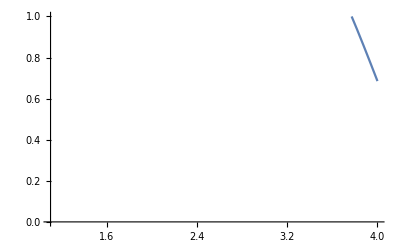

```mathematica
Plot[g2int[x],{x,1.1,4},PlotRange->{0,1}]
```

```mathematica
eta
```

446.16

```mathematica
gsqrt
```

InterpolatingFunction[…]

```mathematica
Length[tabel]
```

4250

```mathematica
tabel[[1]]
```

{0.694598,0.568151,0.528145,0.224884}

0.0000665672

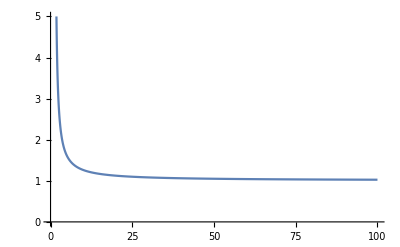

```mathematica
tabel=FundLorentz001;
a0=0.01;
num=4250(*Length[tabel]*);(*PosMcrit[tabel, 0.171/(a0/1.5)]+1500*)
eta=tabel[[num,1]];
phi=tabel[[num,2]];
Mnorm=tabel[[num,3]]/tabel[[num,1]]^(1/2)
coupling=ruleLorentzian;
cost={η->eta,a->a0};
IntPotentialSign[phi,cost,coupling,100,10^-2,10^-6];
Plot[g2int[x],{x,1.5,100},PlotRange->{0,5}]
```

```mathematica
20->2300
```

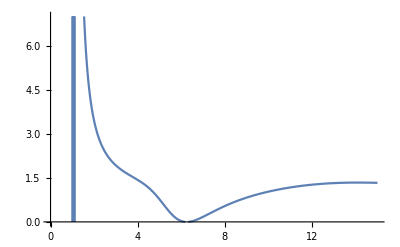

```mathematica
Plot[g2int[x],{x,1.01,15},PlotRange->{0,7}]
```

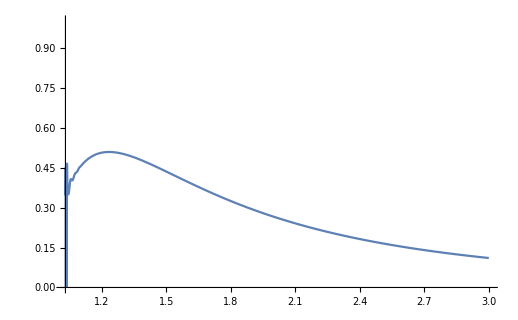

```mathematica
Plot[Veff[x],{x,1.03,3},PlotRange->{0,1}]
```

#### Polynomial coupling

```mathematica
(*(*xmmin=xmed[[Position[Wxmed,Min[Wxmed]][[1]]]]*)
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=100;

wi=0.0001;
wf=0.13;
step=(wf-wi)/pts;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
tab=FundTwoThreeUnst;
ruleCoupling=ruleTwoThree;

xnear=10^-8;
xmax=0.97;
precision=8;


kstart=42;
minima={};

Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
(*k=kstart+10*(l-1);*)
WRON[k]={};
ηk=tab[[k,1]];
λk=tab[[k,2]];
couple={η->ηk,λ->λk};
phihk=tab[[k,3]];

Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSK[phihk,couple,ruleCoupling,ωshoot,xmiddle,xnear,xmax,precision](*[[1,1]]*);
WRON[k]=AppendTo[WRON[k],{ωshoot,check[[1]]}]}
,{j,1,pts}],j];
min=Min[Table[WRON[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WRON[k]//Abs,min][[1,1]];
omegaok=WRON[k][[pos,1]];
minima=AppendTo[minima,{tab[[k,1]],tab[[k,2]],omegaok, tab[[k,4]],tab[[k,5]]}]
,{k,kstart,Length[tab](*IntegerPart[(Length[tab]-kstart)/10]*)}]
,k];*)
```

```mathematica
(*nomefile=StringJoin[{"Data/Stability/FundPhiTwoThreeA3_VItryunstable.dat"}];
Save[nomefile,WROND]*)
```

## Graphics

#### Exponential coupling

M/η^(1/2)=0.0358685 beginning of unstable solutions for Exponential coupling with a=6 and {η,phih,M,Q/M}={429.6,1.17955,0.743439,2.12126}

```mathematica
ListPlot[{WROND[1191]},PlotLabels->{1,2,3}(*,PlotRange->{{2,7},{0,0.5}}*)]
```

-Graphics-

M/η^(1/2)=0.06928561782843319 beginning of unstable solutions for Exponential coupling with a=3 and {η,phih,M,Q/M}={150.,1.54197,0.848572,1.93317}

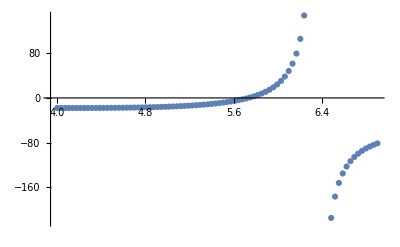

```mathematica
ListPlot[WROND[1249]]
```

```mathematica
tab[[6900]]
```

{84.,2.0779,1.05214,1.64463}

Wronskian as function of ω for Exponential coupling with a = 3/2 (Doneva' s coupling) and for {η, phih, M, Q/M} = {84.`, 2.077903056726155`, 1.0521374551680882`, 1.6446329442789436`}

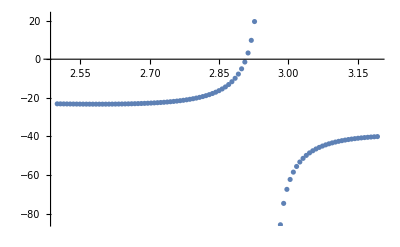

```mathematica
ListPlot[WROND[6900]](**)
```

```mathematica
MsuEta=minima[[All,3]]/minima[[All,1]]^(1/2)
ωiM2sueta=minima[[All,2]]*minima[[All,3]]^2/minima[[All,1]]^(1/2)
```

{0.114798,0.114302}

{0.350633,0.348107}

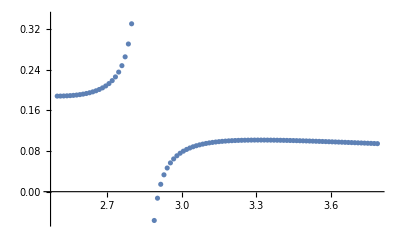

```mathematica
ListPlot[WRON[6900]]
```

Maximum value of mass for a=3/2 for unstable solutions is

```mathematica
tab[[6855,3]]/tab[[6855,1]]^(1/2)
```

0.152425

while Doneva says it is 0.171, but I cannot go to better precision because I get these kind of plots...

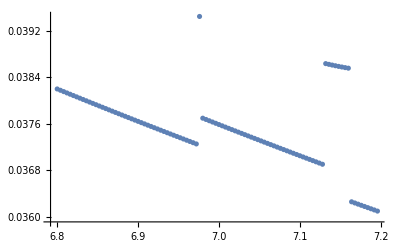

```mathematica
ListPlot[WROND[6848](*,PlotRange->{{2.6,3.3},{0,0.160}}*)]
```

```mathematica
minima[[All,2]]*minima[[All,3]]^2/minima[[All,1]]^(1/2)
```

{0.756381}

Note that as you double the constant “a” that multiplies ϕ^2 to the exponent in the coupling function, the minimum mass beyond which the scalarized solutions are unstable roughly halves.
Then can we claim that starting from the limit given by Doneva of M/η^(1/2)=0.171 with A=3/2, you will get  M_min/η^(1/2)=0.171/multiplier as a becomes a=3/2 * multiplier.
We should keep in mind though that.
Let’s check the dependence of the mass limit for the arising of unstable solutions

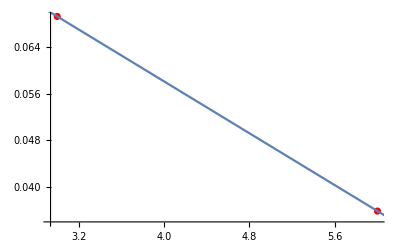

```mathematica
points={(*{1.5,0.15242519443471286},*){3,0.06928561782843319},{6,0.03586848582812391}};
(*fit*)
fit=Fit[points,{1,x},x];
Show[ListPlot[points,PlotStyle->{Red,Thickness[0.02]}],Plot[fit,{x,0,7}]]
```

```mathematica
fit
```

0.102703-0.011139 x

```mathematica
0.16913376043486752-0.023792569829841202 x
```

```mathematica
1/0.011139044000103092
```

89.7743

```mathematica
ReadList["Data/Stability/Fund_unstable_Expo_a=3.dat"];
```

```mathematica
UnstableOme=Table[{minima[[i,3]]/minima[[i,1]]^(1/2),-minima[[i,2]]*minima[[i,3]]^2/minima[[i,1]]^(1/2)},{i,1,Length[minima]}];
verticalline=0.08033973673454155;
```

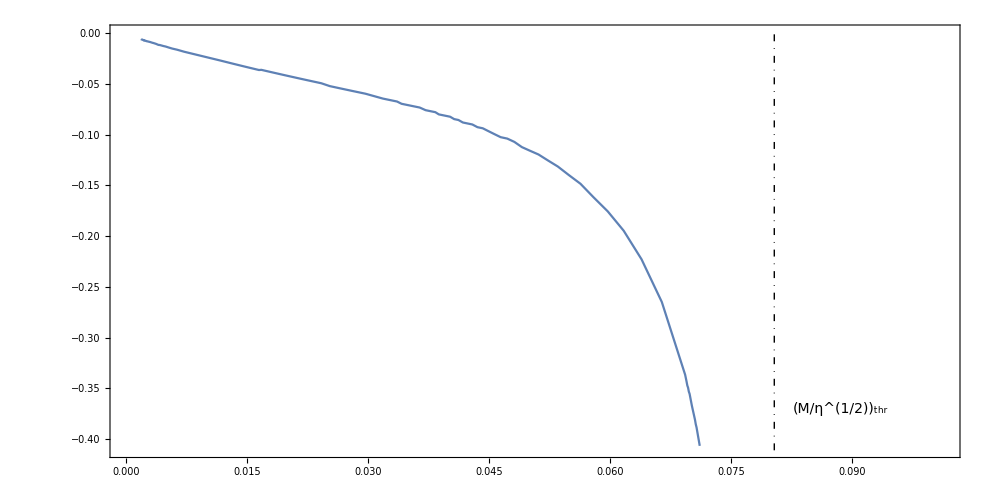
-Graphics--ω_iM^2/η^(1/2)M/η^(1/2)

```mathematica
Labeled[Show[ListLinePlot[UnstableOme,PlotRange->{{0,verticalline+0.021},{-0.41,0}},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],Graphics[{DotDashed,Line[{{verticalline,-0.90},{verticalline,0}}], Text[Style["(M/η^(1/2))_thr",FontSize->14],{verticalline+0.0082,-0.37}]}],
(*ListLinePlot[Legended[QvsMtwothree,"Fund two+three"],PlotStyle->Black,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],
ListLinePlot[Legended[QvsMtwothreeUnst,"Fund two+three unst"],PlotStyle->Gray,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]],*)
PlotLegends->Placed[Automatic,{Top,Left}],ImageSize->10^3],
{Style["-ω_iM^2/η^(1/2)",Thick,FontSize->20],Style["M/η^(1/2)",Thick,FontSize->20]},{Left,Bottom}]
```

#### Polynomial coupling

Plot of the eigenfrequencies of unstable modes against the coupling constant η/(2M)^2 for different coupling functions: ϕ^2+ϕ^3 and simple ϕ^2 and for Schwarzschild solution as well.

```mathematica
ReadList["Data/Stability/FundTwoThree_λ=1η_ultimate.dat"];
ReadList["../Stability/Data/Control/SchwInstability_newBCS.m"];
ReadList["../Stability/Data/Control/FundBranch_GPINTEG_physicalBCK_newBCS.dat"];
SchUnstable2=Table[{minimaSch[[i,1]],-minimaSch[[i,2]]},{i,5,Length[minimaSch]}];
UnstableOmenew=Table[{(minima[[i,1]]/(2minima[[i,3]])^2),-2minima[[i,3]]*minima[[i,2]]},{i,1,Length[minima]}];
```

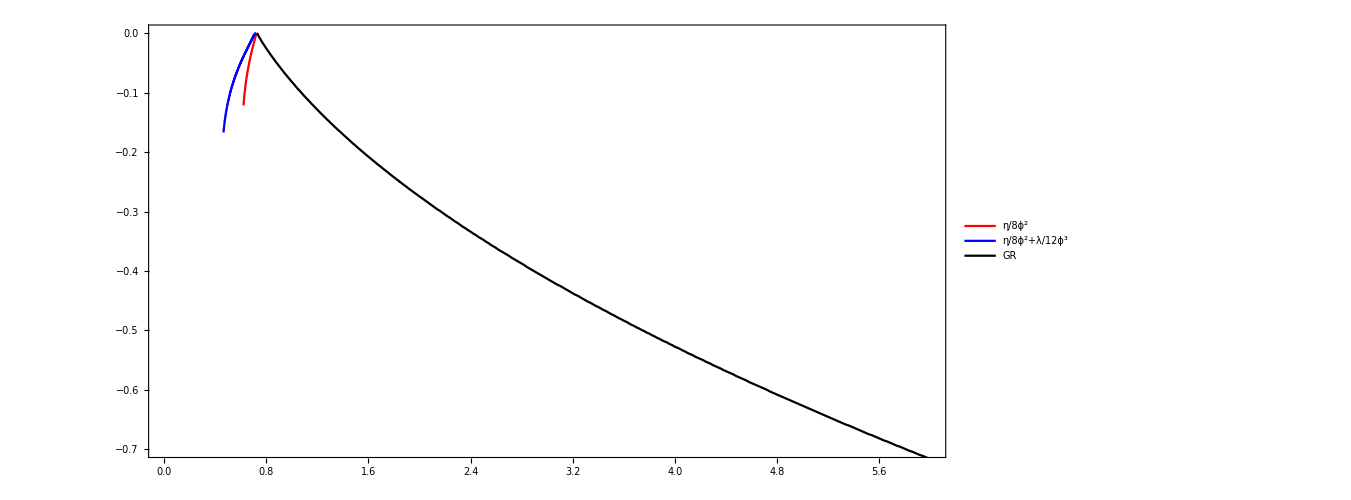
-Graphics--2Mω_iη/(2M)^2

```mathematica
Labeled[Show[
ListLinePlot[Legended[UnstableOmenew,Placed[Style["η/8ϕ^2",FontSize->18],{0.9,0.9}]],PlotStyle->{Red},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,6},{-0.7,0}}],
ListLinePlot[Legended[minimaωvsη23,Placed[Style["η/8ϕ^2+λ/12ϕ^3",FontSize->18],{0.9,0.8}]],PlotStyle->{Blue},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,6},{-0.8,0}}],
ListLinePlot[Legended[SchUnstable2,Placed[Style["GR",FontSize->18],{0.9,0.7}]],PlotStyle->{Black},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,6},{-0.8,0}}],
ImageSize->10^3],
{Style ["-2Mω_i",FontSize->20],Style["η/(2M)^2",FontSize->20]},{Left,Bottom}]
```

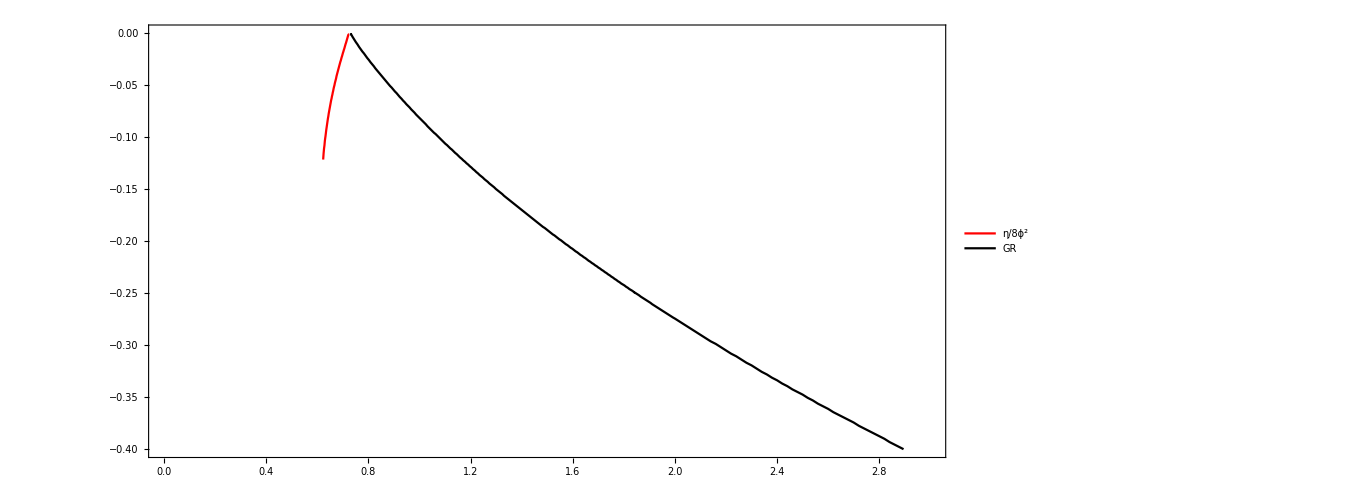
-Graphics--2Mω_iη/(2M)^2

```mathematica
Labeled[Show[
ListLinePlot[Legended[UnstableOmenew,Placed[Style["η/8ϕ^2",FontSize->20],{0.9,0.9}]],PlotStyle->{Red},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,3},{-0.4,0}}],
ListLinePlot[Legended[SchUnstable2,Placed[Style["GR",FontSize->20],{0.9,0.8}]],PlotStyle->{Black},Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,3},{-0.4,0}},
Epilog->{Inset[Column[{Style["Sin[x]",FontColor->Blue],Style["Cos[x]",FontColor->Red]}],Scaled[{0.8,0.8}]]}],
ImageSize->10^3],
{Style["-2Mω_i",FontSize->20],Style["η/(2M)^2",FontSize->20]},{Left,Bottom}]
```